```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/stephan_schiffels/dev/celtic_relationship_analysis

```mathematica
CreateDirectory["Figures"]
```

CreateDirectory::eexist: /Users/stephan_schiffels/dev/celtic_relationship_analysis/Figures already exists.

$Failed

## Birth date simulations

```mathematica
hochdorfBurialDateDist=NormalDistribution[-530,6];
aspergBurialDateDist=NormalDistribution[-490,6];
```

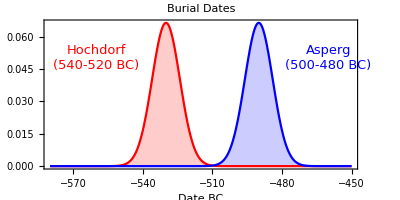

```mathematica
p=Plot[{
PDF[hochdorfBurialDateDist,x],
PDF[aspergBurialDateDist,x]
},{x,-580,-450},PlotStyle->{Red,Blue},Frame->{True,False,False,False}, Filling->Automatic,PlotRange->All,
FrameLabel->{"Date BC",None},
Epilog->{
Text[Style["Hochdorf\n(540-520 BC)",Red,13],{-560,0.05}],
Text[Style["Asperg\n(500-480 BC)",Blue,13],{-460,0.05}]
},
PlotLabel->"Burial Dates",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/burialDates.pdf",p]
```

Figures/burialDates.pdf

```mathematica
hochdorfAgeDist=NormalDistribution[45,6];
aspergAgeDist=NormalDistribution[30,6];
```

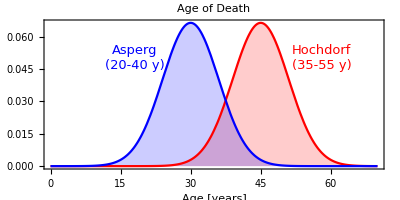

```mathematica
p=Plot[{
PDF[hochdorfAgeDist,x],
PDF[aspergAgeDist,x]
},{x,0,70},PlotStyle->{Red,Blue},Filling->Automatic,PlotRange->All,
Frame->{True,False,False,False},
FrameLabel->{"Age [years]",None},
Epilog->{
Text[Style["Hochdorf\n(35-55 y)",Red,13],{58,0.05}],
Text[Style["Asperg\n(20-40 y)",Blue,13],{18,0.05}]
},
PlotLabel->"Age of Death",AspectRatio->1/2]
```

```mathematica
Export["Figures/ages.pdf",p]
```

Figures/ages.pdf

```mathematica
n=10000;
hochdorfBirthDateSamples=RandomVariate[hochdorfBurialDateDist,n]-RandomVariate[hochdorfAgeDist,n];
aspergBirthDateSamples=RandomVariate[aspergBurialDateDist,n]-RandomVariate[aspergAgeDist,n];
```

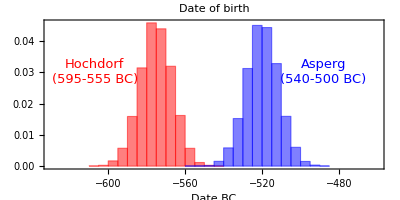

```mathematica
p=Histogram[{hochdorfBirthDateSamples,aspergBirthDateSamples},Automatic,"PDF",PlotRange->{{-630,-460},All},ChartStyle->{Red,Blue},
Frame->{True,False,False,False},
FrameLabel->{"Date BC",None},
Epilog->{
Text[Style["Hochdorf\n(595-555 BC)",Red,13],{-607,0.03}],
Text[Style["Asperg\n(540-500 BC)",Blue,13],{-488,0.03}]
},
PlotLabel->"Date of birth",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/birthDates.pdf",p]
```

Figures/birthDates.pdf

```mathematica
Quantile[hochdorfBirthDateSamples,{0.01,0.99}]
Quantile[aspergBirthDateSamples,{0.01,0.99}]
```

{-594.964,-556.097}

{-539.658,-500.127}

```mathematica
mothersAgeDist=NormalDistribution[30,6];
```

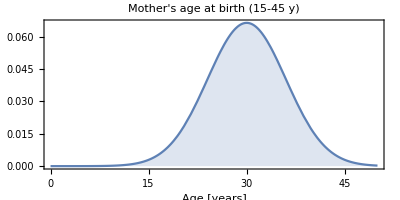

```mathematica
p=Plot[PDF[mothersAgeDist,x],{x,0,50},Filling->Automatic,
Frame->{True,False,False,False},
FrameLabel->{"Age [years]",None},
PlotLabel->"Mother's age at birth (15-45 y)",
AspectRatio->1/2
]
```

```mathematica
Export["Figures/mothersAge.pdf",p]
```

Figures/mothersAge.pdf

## Sibling model formulas

p[Age_H]~NormalDistribution[45,6]
p[Age_A]~NormalDistribution[30,6]